```mathematica
(*Definición del Negative I*)NegativeFeedbackFull={P'[t]==-kon*P[t]*T[t]+koff*(C0[t]+C1[t]+C2[t]+C3[t]+C4[t]+C5[t]),T'[t]==-kon*P[t]*T[t]+koff*(C0[t]+C1[t]+C2[t]+C3[t]+C4[t]+C5[t]),C0'[t]==kon*P[t]*T[t]-(koff+kp)*C0[t]+(b+gamma*S[t])*C1[t],C1'[t]==kp*C0[t]-(koff+kp+b+gamma*S[t])*C1[t]+(b+gamma*S[t])*C2[t],C2'[t]==kp*C1[t]-(koff+kp+b+gamma*S[t])*C2[t]+(b+gamma*S[t])*C3[t],C3'[t]==kp*C2[t]-(koff+kp+b+gamma*S[t])*C3[t]+(b+gamma*S[t])*C4[t],C4'[t]==kp*C3[t]-(koff+kp+b+gamma*S[t])*C4[t]+(b+gamma*S[t])*C5[t],C5'[t]==kp*C4[t]-(koff+b+gamma*S[t])*C5[t],S'[t]==alpha*C1[t]*(ST-S[t])-beta*S[t]};
```

```mathematica
(*Condiciones iniciales*)initialConditionsFull={P[0]==100,T[0]==2*10^4,C0[0]==0,C1[0]==0,C2[0]==0,C3[0]==0,C4[0]==0,C5[0]==0,S[0]==0};
```

```mathematica
parametersFull={kon->5*10^-5,koff->0.01,kp->1,b->0.04,gamma->4.4*10^-4,ST->6*10^5,alpha->2*10^-4,beta->1};
```

```mathematica
solutionFull=NDSolve[Join[NegativeFeedbackFull/. parametersFull,initialConditionsFull],{P,T,C0,C1,C2,C3,C4,C5,S},{t,0,100},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6];
```

```mathematica
C5sol=C5/. solutionFull[[1]];
```

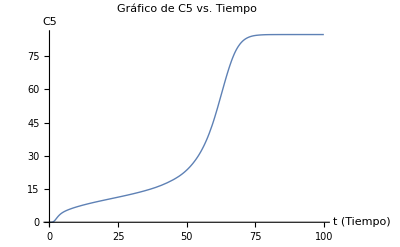

```mathematica
Plot[C5sol[t], {t, 0, 100}, 
 PlotRange -> All, 
 AxesLabel -> {"t (Tiempo)", "C5"}, 
 PlotLabel -> "Gráfico de C5 vs. Tiempo", 
 PlotStyle -> Thick]
```

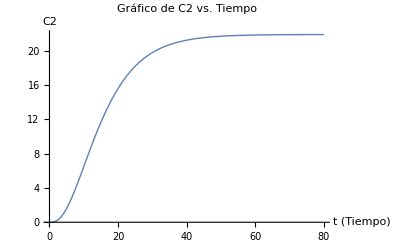

```mathematica
(*NEGATIVE CON N = 2*)odeModel={P'[t]==-kon*P[t]*T[t]+koff*C0[t]+koff*C1[t]+koff*C2[t],T'[t]==-kon*P[t]*T[t]+koff*C0[t]+koff*C1[t]+koff*C2[t],C0'[t]==kon*P[t]*T[t]-(koff+kp)*C0[t]+(b+gamma*S[t])*C1[t],C1'[t]==kp*C0[t]-(koff+kp+b+gamma*S[t])*C1[t]+(b+gamma*S[t])*C2[t],C2'[t]==kp*C1[t]-(koff+b+gamma*S[t])*C2[t],S'[t]==alpha*C1[t]*(ST-S[t])-beta*S[t]};

(*Parámetros*)
parametersFull={kon->1/100000,koff->1/20,kp->9/100,b->1/25,gamma->1/1000000,ST->6*10^5,alpha->2*10^-4,beta->1};

(*Condiciones iniciales*)
initialConditions={P[0]==100,T[0]==2*10^4,C0[0]==0,C1[0]==0,C2[0]==0,S[0]==0};

(*Resolver el sistema*)
solution=NDSolve[Join[odeModel/. parametersFull,initialConditions],{P,T,C0,C1,C2,S},{t,0,80},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6];
C2sol=C2/. solution[[1]];(*Extraer la solución para C2*)Plot[C2sol[t],{t,0,80},PlotRange->All,AxesLabel->{"t (Tiempo)","C2"},PlotLabel->"Gráfico de C2 vs. Tiempo",PlotStyle->Thick]
```

```mathematica
n=5000;
logeado=Subdivide[0,7,n-1];(*Genera n puntos entre 0 y 6*)
LT=10^logeado;
```

```mathematica
respuestaSteadyState=Table[Module[{x0,solution,C2sol},(*Definir condiciones iniciales para este valor de LT*)x0={P[0]==LT[[i]],T[0]==10,C0[0]==0,C1[0]==0,C2[0]==0,S[0]==0};
(*Resolver el sistema para este valor inicial*)solution=NDSolve[Join[odeModel/. parametersFull,x0],{P,T,C0,C1,C2,S},{t,0,20},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6];
(*Extraer la solución para C2*)C2sol=C2/. solution[[1]];
(*Evaluar el valor máximo de C2 en el intervalo*)Max[Evaluate[C2sol[t]/. t->Subdivide[0,20,1000]]]],{i,1,n}];
```

```mathematica
LTlog = Log10[LT];
```

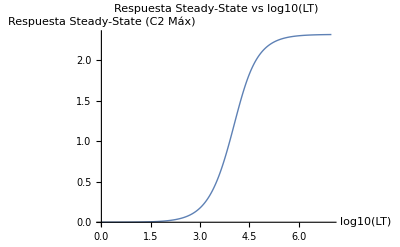

```mathematica
ListLinePlot[
 Transpose[{LTlog, respuestaSteadyState}], 
 AxesLabel -> {"log10(LT)", "Respuesta Steady-State (C2 Máx)"}, 
 PlotLabel -> "Respuesta Steady-State vs log10(LT)", 
 PlotStyle -> Thick
]
```

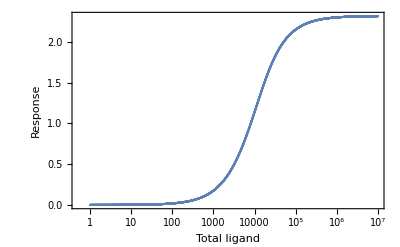

```mathematica
ListLogLinearPlot[Transpose[{10^LTlog,respuestaSteadyState}],Frame->True,FrameLabel->{"Total ligand","Response"},PlotStyle->{Thickness[0.5]},(*Grosor personalizado y color rojo*)Mesh->None,LabelStyle->{Bold,14}]
```

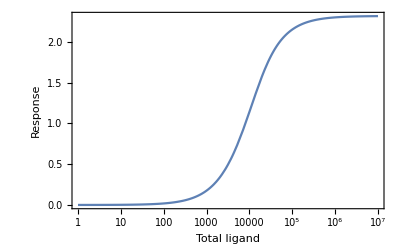

```mathematica
(*Crear la función interpolada a partir de los datos*)interpolacion=Interpolation[Transpose[{10^LTlog,respuestaSteadyState}]];

(*Usar LogLinearPlot para graficar la función interpolada con etiquetas personalizadas*)
LogLinearPlot[interpolacion[x],{x,Min[10^LTlog],Max[10^LTlog]},PlotRange->All,Frame->True,FrameLabel->{"Total ligand","Response"},LabelStyle->{Bold,14},FrameTicks->{{{1,"1"},{100,"100"},{10^4,"10^4"},{10^6,"10^6"}},(*Eje x*)Automatic (*Eje y:etiquetas automáticas*)}]
```